```mathematica
data = First[Import["import_data_6.xlsx"]]
```

{{1.,1.,5.11},{1.,1.,7.04},{1.,1.,4.84},{1.,1.,8.76},{1.,1.,8.56},{1.,2.,6.1},{1.,2.,9.35},{1.,2.,8.84},{1.,3.,7.31},{1.,3.,8.49},{1.,4.,7.94},{1.,4.,10.29},{1.,4.,11.69},{2.,1.,2.65},{2.,1.,6.76},{2.,1.,3.09},{2.,1.,7.12},{2.,2.,8.},{2.,2.,8.28},{2.,2.,5.86},{2.,3.,6.8},{2.,3.,7.97},{2.,3.,5.99},{2.,3.,5.8},{2.,3.,6.53},{2.,4.,5.52},{2.,4.,8.82},{2.,4.,6.74},{2.,4.,7.11},{2.,4.,3.8}}

```mathematica
factorA=data[[All,{1,3}]]
```

{{1.,5.11},{1.,7.04},{1.,4.84},{1.,8.76},{1.,8.56},{1.,6.1},{1.,9.35},{1.,8.84},{1.,7.31},{1.,8.49},{1.,7.94},{1.,10.29},{1.,11.69},{2.,2.65},{2.,6.76},{2.,3.09},{2.,7.12},{2.,8.},{2.,8.28},{2.,5.86},{2.,6.8},{2.,7.97},{2.,5.99},{2.,5.8},{2.,6.53},{2.,5.52},{2.,8.82},{2.,6.74},{2.,7.11},{2.,3.8}}

```mathematica
responseA=factorA[[All, 2]];
```

```mathematica
factorB=data[[All,{2,3}]]
```

{{1.,5.11},{1.,7.04},{1.,4.84},{1.,8.76},{1.,8.56},{2.,6.1},{2.,9.35},{2.,8.84},{3.,7.31},{3.,8.49},{4.,7.94},{4.,10.29},{4.,11.69},{1.,2.65},{1.,6.76},{1.,3.09},{1.,7.12},{2.,8.},{2.,8.28},{2.,5.86},{3.,6.8},{3.,7.97},{3.,5.99},{3.,5.8},{3.,6.53},{4.,5.52},{4.,8.82},{4.,6.74},{4.,7.11},{4.,3.8}}

```mathematica
responseB=factorB[[All, 2]];
```

Запишем значения откликов для i-ой группы факторов А и В

```mathematica
firstGroupA = grupsOfFactorA[[1]]
secondGroupA = grupsOfFactorA[[2]]
```

{{1.,5.11},{1.,7.04},{1.,4.84},{1.,8.76},{1.,8.56},{1.,6.1},{1.,9.35},{1.,8.84},{1.,7.31},{1.,8.49},{1.,7.94},{1.,10.29},{1.,11.69}}

{{2.,2.65},{2.,6.76},{2.,3.09},{2.,7.12},{2.,8.},{2.,8.28},{2.,5.86},{2.,6.8},{2.,7.97},{2.,5.99},{2.,5.8},{2.,6.53},{2.,5.52},{2.,8.82},{2.,6.74},{2.,7.11},{2.,3.8}}

```mathematica
firstGroupB = grupsOfFactorB[[1]]
secondGroupB = grupsOfFactorB[[2]]
thirdGroupB = grupsOfFactorB[[3]]
fourthGroupB = grupsOfFactorB[[4]]
```

{{1.,5.11},{1.,7.04},{1.,4.84},{1.,8.76},{1.,8.56},{1.,2.65},{1.,6.76},{1.,3.09},{1.,7.12}}

{{2.,6.1},{2.,9.35},{2.,8.84},{2.,8.},{2.,8.28},{2.,5.86}}

{{3.,7.31},{3.,8.49},{3.,6.8},{3.,7.97},{3.,5.99},{3.,5.8},{3.,6.53}}

{{4.,7.94},{4.,10.29},{4.,11.69},{4.,5.52},{4.,8.82},{4.,6.74},{4.,7.11},{4.,3.8}}

Найдем среднее значение отклика для  i-ой группы

```mathematica
θA1=Mean[firstGroupA[[All,2]]]
θA2=Mean[secondGroupA[[All,2]]]
```

8.02462

6.28471

```mathematica
θB1=Mean[firstGroupB[[All,2]]]
θB2=Mean[secondGroupB[[All,2]]]
θB3=Mean[thirdGroupB[[All,2]]]
θB4=Mean[fourthGroupB[[All,2]]]
```

5.99222

7.73833

6.98429

7.73875

Запишем матрицы неполного ранга для факторов A и В

```mathematica
lenA1=Length[firstGroupA];
lenA2=Length[secondGroupA];
```

```mathematica
lenB1=Length[firstGroupB];
lenB2=Length[secondGroupB ];
lenB3=Length[thirdGroupB];
lenB4=Length[fourthGroupB ];
```

```mathematica
lenA=lenA1+lenA2;
```

```mathematica
col1=Table[1,{i,lenA}];
col2=Table[If[i>lenA1,0,1],{i,lenA}];
col3=Table[If[i<=lenA1,0,1],{i,lenA}];
```

```mathematica
XA=Transpose[{col1,col2,col3}]
```

{{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1},{1,0,1}}

```mathematica
lenB=lenB1+lenB2+lenB3+lenB4;
```

```mathematica
col1=Table[1,{i,lenB}];
col2=Table[If[i>lenB1  ,0,1],{i,lenB}];
col3=Table[If[i>lenB1 && i<lenB2+lenB1 ,1,0],{i,lenB}];
col4=Table[If[i>=lenB2+lenB1 && i<lenB3+lenB2 +lenB1 ,1,0],{i,lenB}];
col5=Table[If[i>=lenB3+lenB2+lenB1 && i<=lenB,1,0],{i,lenB}];
```

```mathematica
XB=Transpose[{col1,col2,col3,col4,col5}]
```

{{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,0,1,0,0},{1,0,1,0,0},{1,0,1,0,0},{1,0,1,0,0},{1,0,1,0,0},{1,0,0,1,0},{1,0,0,1,0},{1,0,0,1,0},{1,0,0,1,0},{1,0,0,1,0},{1,0,0,1,0},{1,0,0,1,0},{1,0,0,0,1},{1,0,0,0,1},{1,0,0,0,1},{1,0,0,0,1},{1,0,0,0,1},{1,0,0,0,1},{1,0,0,0,1},{1,0,0,0,1},{1,0,0,0,1}}

Получим модель полного ранга, добавив ограничения α_k= 0

Найдем параметры модели для фактора А

```mathematica
θA0=θA2
αA1= θA1-θA0
XAnew=Transpose[Drop[Transpose[XA],-1]]
```

6.28471

1.73991

{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}

```mathematica
YA=XAnew.{θA0,αA1};
```

Найдем параметры модели для фактора В

```mathematica
θB0=θB4;
αB1= θB1-θB0;
αB2= θB2-θB0;
αB3= θB3-θB0;
XBnew=Transpose[Drop[Transpose[XB],-1]];
```

```mathematica
YB=XBnew.{θB0,αB1,αB2,αB3};
```

Найдем оценки параметров модели для факторов А и В

```mathematica
θA = Inverse[Transpose[XAnew].XAnew].Transpose[XAnew].YA
```

{6.28471,1.73991}

```mathematica
θB=Inverse[Transpose[XBnew].XBnew].Transpose[XBnew].YB
```

{7.73875,-1.74653,-0.000416667,-0.754464}

Найдем сумму квадратов остатков для двух моделей

```mathematica
SSRA = Transpose[responseA].responseA-Transpose[responseA].XAnew.θA
```

94.8677

```mathematica
SSRB = Transpose[responseB].responseB-Transpose[responseB].XBnew.θB
```

119.107

Найдем остатки модели для факторов A и B

```mathematica
RA=responseA-YA
RB=responseB-YB
```

{-2.91462,-0.984615,-3.18462,0.735385,0.535385,-1.92462,1.32538,0.815385,-0.714615,0.465385,-0.0846154,2.26538,3.66538,-3.63471,0.475294,-3.19471,0.835294,1.71529,1.99529,-0.424706,0.515294,1.68529,-0.294706,-0.484706,0.245294,-0.764706,2.53529,0.455294,0.825294,-2.48471}

{-0.882222,1.04778,-1.15222,2.76778,2.56778,0.107778,3.35778,2.84778,1.31778,0.751667,0.201667,2.55167,3.95167,-5.08833,-0.224286,-3.89429,0.135714,1.01571,1.29571,-1.12429,-0.184286,0.23125,-1.74875,-1.93875,-1.20875,-2.21875,1.08125,-0.99875,-0.62875,-3.93875}

Проверка на однородность дисперсии остатков и на нормальность остатков первой модели

```mathematica
data1=RA[[1;;lenA1]];
data2=RA[[lenA1;;]];
```

Критерий Бартлетта о равенстве дисперсий

```mathematica
VarianceEquivalenceTest[{data1,data2},"Bartlett"]
```

0.923993

Таким образом, принимаем гипотезу H0 о равенстве дисперсий

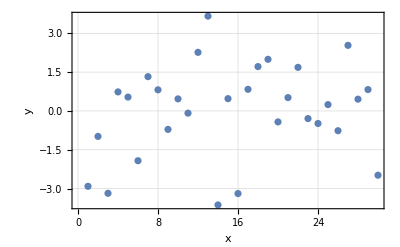

```mathematica
ListPlot[RA,Frame->True,FrameLabel->{"x","y"},PlotLegends->"Expressions",GridLines->Automatic]
```

Проверка на нормальность

```mathematica
infA = DistributionFitTest[RA,Automatic,"HypothesisTestData"];
infA["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.55987 | 0.148428
Baringhaus-Henze | 0.41844 | 0.126395
Cramér-von Mises | 0.0923569 | 0.141398
Jarque-Bera ALM | 0.881227 | 0.578112
Kolmogorov-Smirnov | 0.13437 | 0.18112
Kuiper | 0.18698 | 0.222037
Mardia Combined | 0.881227 | 0.578112
Mardia Kurtosis | -0.398776 | 0.690058
Mardia Skewness | 0.679031 | 0.40992
Pearson χ^2 | 4.13333 | 0.530383
Shapiro-Wilk | 0.95779 | 0.271705
Watson U^2 | 0.0858185 | 0.145493

Таким образом, принимаем гипотезу о том, что данные распределены нормальным образом

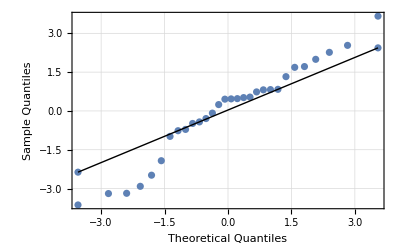

```mathematica
QuantilePlot[RA,Frame->True,FrameLabel->{"Theoretical Quantiles","Sample Quantiles"},PlotLegends->"Expressions",GridLines->Automatic]
```

Проверка на однородность дисперсии остатков и на нормальность остатков второй модели

```mathematica
data1=RB[[1;;lenB1]];
data2=RB[[lenB1;;lenB1+lenB2]];
data3=RB[[lenB1+lenB2;;lenB1+lenB2+lenB3]];
data4=RB[[lenB1+lenB2+lenB3;;lenB]];
```

Критерий Бартлетта о равенстве дисперсий

```mathematica
VarianceEquivalenceTest[{data1,data2,data3,data4},"Bartlett"]
```

0.273286

Таким образом, принимаем гипотезу H0 о равенстве дисперсий

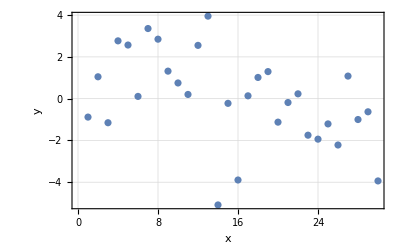

```mathematica
ListPlot[RB,Frame->True,FrameLabel->{"x","y"},PlotLegends->"Expressions",GridLines->Automatic]
```

Проверка на нормальность

```mathematica
infB=DistributionFitTest[RB,Automatic,"HypothesisTestData"];
infB["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.265819 | 0.709617
Baringhaus-Henze | 0.08761 | 0.83936
Cramér-von Mises | 0.0324504 | 0.810475
Jarque-Bera ALM | 0.648789 | 0.681764
Kolmogorov-Smirnov | 0.0863729 | 0.826729
Kuiper | 0.12235 | 0.817502
Mardia Combined | 0.648789 | 0.681764
Mardia Kurtosis | -0.196897 | 0.843908
Mardia Skewness | 0.532221 | 0.465675
Pearson χ^2 | 7.33333 | 0.197007
Shapiro-Wilk | 0.974718 | 0.674412
Watson U^2 | 0.0305617 | 0.842439

Таким образом, принимаем гипотезу о том, что данные распределены нормальным образом

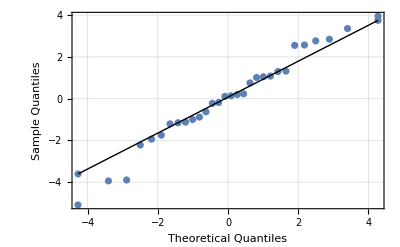

```mathematica
QuantilePlot[RB,Frame->True,FrameLabel->{"Theoretical Quantiles","Sample Quantiles"},PlotLegends->"Expressions",GridLines->Automatic]
```

Составим сумму квадратов, обусловленной гипотезой H0 для первой модели

```mathematica
CTA={0,1};
```

```mathematica
inv=CTA.Inverse[Transpose[XAnew].XAnew].Transpose[CTA];
```

```mathematica
SSH0A=θA.Transpose[CTA]*1/inv*CTA.θA;
```

```mathematica
FsA=(30-2)/1*SSH0A/SSRA
```

6.58209

```mathematica
FthA=1-CDF[FRatioDistribution[1,30-2],FsA]
```

0.015945

```mathematica
Quantile[FRatioDistribution[1,30-2],0.95]
```

4.19597

Таким образом, отвергаем гипотезу H0 о равенстве всех параметрах модели 0. Т.е. параметры модели попарно различны

Составим сумму квадратов, обусловленной гипотезой H0 для второй модели

```mathematica
CTB=Transpose[{{0,0,0},{1,0,0},{0,1,0},{0,0,1}}];
```

```mathematica
SSH0B=θB.Transpose[CTB].Inverse[CTB.Inverse[Transpose[XBnew].XBnew].Transpose[CTB]].CTB.θB;
```

```mathematica
FsB=(30-4)/1*SSH0B/SSRB
```

3.65305

```mathematica
FthB=1-CDF[FRatioDistribution[1,30-4],FsB]
```

0.0670496

```mathematica
Quantile[FRatioDistribution[1,30-4],0.95]
```

4.2252

Таким образом, отвергнуть гипотезу H0 о равенстве всех параметров модели 0 не можем. Т.е все параметры модели одинаковые

Сравним средние для второй модели

```mathematica
MSRB=SSRB/(30-4);
```

```mathematica
t12=(θB1-θB2)/(√(MSRB*(1/lenB1+1/lenB2)));
Tth12=Quantile[StudentTDistribution[30-4],1-0.05/2];
If[Abs[t12]>Tth12,Print[True],Print[False]]
```

False

```mathematica
t13=(θB1-θB3)/(√(MSRB*(1/lenB1+1/lenB3)));
Tth13=Quantile[StudentTDistribution[30-4],1-0.05/2];
If[Abs[t13]>Tth13,Print[True],Print[False]]
```

False

```mathematica
t14=(θB1-θB4)/(√(MSRB*(1/lenB1+1/lenB4)));
Tth14=Quantile[StudentTDistribution[30-4],1-0.05/2];
If[Abs[t14]>Tth14,Print[True],Print[False]]
```

False

```mathematica
t23=(θB2-θB3)/(√(MSRB*(1/lenB2+1/lenB3)));
Tth23=Quantile[StudentTDistribution[30-4],1-0.05/2];
If[Abs[t23]>Tth23,Print[True],Print[False]]
```

False

```mathematica
t24=(θB2-θB4)/(√(MSRB*(1/lenB2+1/lenB4)));
Tth24=Quantile[StudentTDistribution[30-4],1-0.05/2];
If[Abs[t24]>Tth24,Print[True],Print[False]]
```

False

```mathematica
t34=(θB3-θB4)/(√(MSRB*(1/lenB3+1/lenB4)));
Tth34=Quantile[StudentTDistribution[30-4],1-0.05/2];
If[Abs[t34]>Tth34,Print[True],Print[False]]
```

False

Все верно. Получили при попарном сравнение,что все средние равны во второй модели.